```mathematica
g[prob_]:=If [prob<=0.001021453702391378,32,
If[ prob<=0.004151650554233785&& prob>0.001021453702391378 , 
(-584.962260272084*prob+10.13570866882117),
 If[prob<=0.01359667098324998&&prob>0.004151650554233785  ,
(-192.6450521799878*prob+8.506944714410169),
 If[prob<=0.05399137458004444&&prob>0.01359667098324998  ,
(-50.62607129324977*prob+6.575959357916722),
 If[prob<=0.1420480516058986&&prob>0.05399137458004444  ,
(-11.87410019056137*prob+4.483687170396419),
 If[prob<=0.2463455066216964&&prob>0.1420480516058986  ,
(-8.613130253286352*prob+4.020472744461092),
 If[prob<=0.595815289564374&&prob>0.2463455066216964  ,
(-3.761918786389538*prob+2.825398597919413),
 If[prob<=0.998000001&&prob>0.595815289564374  ,
(-1.444862453710759*prob+1.44486100812744),
0]]]]]]]]

f[prob_]:=Floor[g[prob]*100]
```

```mathematica
g2[prob_]:=If [prob<0.000001 ,32,
If[ prob<=0.001&& prob>=0.000001 ,
(-9975.760016613431*prob+19.941568569324174),
If[ prob<=0.004&& prob>0.001 ,
(-666.6666666666666*prob+10.632117027821168),
If[ prob<=0.014&& prob>0.004 ,
(-180.7354922057604*prob+8.688392330171544),
If[ prob<=0.053&& prob>0.014 ,
(-49.245176838301244*prob+6.847528111047116),
If[ prob<=0.142&& prob>0.053 ,
(-15.975699686667065*prob+5.084849116337398),
If[ prob<=0.246&& prob>0.142 ,
(-7.623299489760664*prob+3.8980664880404327),
If[ prob<=0.595&& prob>0.246 ,
(-3.650898441241519*prob+2.920984031604402),
If[ prob<=0.998&& prob>0.595 ,
(-1.8505238404281055*prob+1.849048341716919),
0]]]]]]]]]

f2[prob_]:=Floor[g2[prob]*100]
```

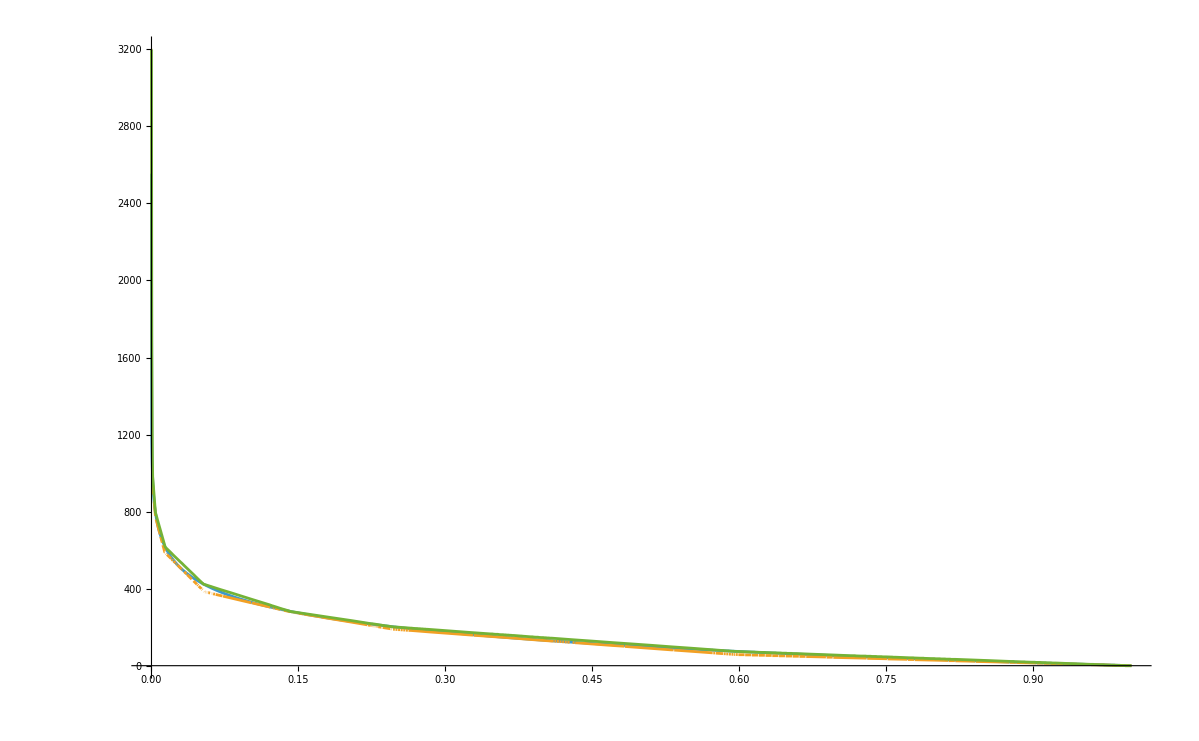

```mathematica
Plot[{-100Log[2,x],f[x],f2[x]},{x,0,1},PlotRange->All]
```

```mathematica
`
```